```mathematica
Needs["Utilities`"]
Needs["Dielectrics`"]
Needs["Constants`"]
Needs["OpticalFits`"]
Needs["EnergyLoss`"]
```

#### Load Fit Parameters

```mathematica
FeTotalparams =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparams"];
(*FeTotalparamsExtrapolatedν =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparamsExtrapolatedν"];
FeTotalparamsExtrapolatedνn =ReadIt[NotebookDirectory[]<>"../extract optical data/FeTotalparamsExtrapolatedνn"];*)
SiO2Totalparams= ReadIt[NotebookDirectory[]<>"../extract optical data/SiO2Totalparams"];
MgOTotalparams =ReadIt[NotebookDirectory[]<>"../extract optical data/MgOTotalparams"];
```

### with wider mass range and temperature enhancement

Also changed velocity bounds so they are above escape velocity while we compute κ_min

```mathematica
vescape
{2 10^-4,2 10^-1} "c" /.SIConstRepl
```

11200

{60000,60000000}

#### Run Iron

```mathematica
FeTotalparamscoreT={{},{},{},{},{},{}};
Do[FeTotalparamscoreT[[i]]=Utilities`ReplaceParams[FeTotalparams[[i]],βcore,"β"],{i,Length[FeTotalparams]}];
```

```mathematica
FeELOutputDictSIEnhancedTest= EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,FeTotalparamscoreT,True,"FeELOutputDictSIEnhancedTest"]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000334844 and 3.4852×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000334844 
Prefactor:	1.28051×10^14
dEdr:	4.28772×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000269583 and 0.0000153292 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000269583 
Prefactor:	9.67268×10^13
dEdr:	2.60759×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {7257.97}. NIntegrate obtained 0.000177397 and 0.000012255 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000177397 
Prefactor:	1.59371×10^15
dEdr:	2.8272×10^11

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000490278 
Prefactor:	1.37274×10^16
dEdr:	6.73024×10^11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 60000
L:	3.02195×10^-6 
Prefactor:	7.48944×10^16
dEdr:	2.26327×10^11

For mχ = 4.45×10^-33 , vχ = 60000
L:	2.22176×10^-7 
Prefactor:	4.85342×10^16
dEdr:	1.07831×10^10

dEdr total: 1.26181×10^12

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00304034 
Prefactor:	1.28051×10^12
dEdr:	3.89319×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00275526 
Prefactor:	9.67268×10^11
dEdr:	2.66508×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00149143 
Prefactor:	1.59371×10^13
dEdr:	2.37691×10^10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000490222 
Prefactor:	1.37274×10^14
dEdr:	6.72947×10^10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000030256 
Prefactor:	7.48944×10^14
dEdr:	2.26601×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	2.22178×10^-6 
Prefactor:	4.85342×10^14
dEdr:	1.07832×10^9

dEdr total: 1.2136×10^11

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0332471 
Prefactor:	1.28051×10^10
dEdr:	4.25734×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.02625 
Prefactor:	9.67268×10^9
dEdr:	2.53908×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0157121 
Prefactor:	1.59371×10^11
dEdr:	2.50406×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00491162 
Prefactor:	1.37274×10^12
dEdr:	6.74238×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00030389 
Prefactor:	7.48944×10^12
dEdr:	2.27597×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0000222209 
Prefactor:	4.85342×10^12
dEdr:	1.07847×10^8

dEdr total: 1.23099×10^10

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.678019 
Prefactor:	1.28051×10^8
dEdr:	8.68213×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.561138 
Prefactor:	9.67268×10^7
dEdr:	5.42771×10^7

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.311906 
Prefactor:	1.59371×10^9
dEdr:	4.97088×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.053064 
Prefactor:	1.37274×10^10
dEdr:	7.2843×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.00304627 
Prefactor:	7.48944×10^10
dEdr:	2.28148×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.000222098 
Prefactor:	4.85342×10^10
dEdr:	1.07794×10^7

dEdr total: 1.60554×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0015167 
Prefactor:	1.28051×10^14
dEdr:	1.94216×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00122727 
Prefactor:	9.67268×10^13
dEdr:	1.1871×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000748723 
Prefactor:	1.59371×10^15
dEdr:	1.19325×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000224677 
Prefactor:	1.37274×10^16
dEdr:	3.08423×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.0000145461 
Prefactor:	7.48944×10^16
dEdr:	1.08942×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	1.09019×10^-6 
Prefactor:	4.85342×10^16
dEdr:	5.29116×10^10

dEdr total: 5.73275×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0151484 
Prefactor:	1.28051×10^12
dEdr:	1.93977×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0122604 
Prefactor:	9.67268×10^11
dEdr:	1.18591×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00748223 
Prefactor:	1.59371×10^13
dEdr:	1.19245×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0022462 
Prefactor:	1.37274×10^14
dEdr:	3.08345×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.000145457 
Prefactor:	7.48944×10^14
dEdr:	1.08939×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0000109019 
Prefactor:	4.85342×10^14
dEdr:	5.29115×10^9

dEdr total: 5.73078×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.166174 
Prefactor:	1.28051×10^10
dEdr:	2.12788×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.117227 
Prefactor:	9.67268×10^9
dEdr:	1.1339×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0717915 
Prefactor:	1.59371×10^11
dEdr:	1.14415×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0219851 
Prefactor:	1.37274×10^12
dEdr:	3.01798×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00145078 
Prefactor:	7.48944×10^12
dEdr:	1.08655×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.00010899 
Prefactor:	4.85342×10^12
dEdr:	5.28973×10^8

dEdr total: 5.62776×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.64738 
Prefactor:	1.28051×10^8
dEdr:	2.10949×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.35427 
Prefactor:	9.67268×10^7
dEdr:	1.30994×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.931225 
Prefactor:	1.59371×10^9
dEdr:	1.48411×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.355917 
Prefactor:	1.37274×10^10
dEdr:	4.88581×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.0173792 
Prefactor:	7.48944×10^10
dEdr:	1.3016×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.00106315 
Prefactor:	4.85342×10^10
dEdr:	5.15991×10^7

dEdr total: 8.06507×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00207932 
Prefactor:	1.28051×10^14
dEdr:	2.66259×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00141753 
Prefactor:	9.67268×10^13
dEdr:	1.37114×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000922281 
Prefactor:	1.59371×10^15
dEdr:	1.46985×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000300739 
Prefactor:	1.37274×10^16
dEdr:	4.12836×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.0000142552 
Prefactor:	7.48944×10^16
dEdr:	1.06764×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	7.22746×10^-7 
Prefactor:	4.85342×10^16
dEdr:	3.50779×10^10

dEdr total: 7.1043×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0251229 
Prefactor:	1.28051×10^12
dEdr:	3.21702×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.016317 
Prefactor:	9.67268×10^11
dEdr:	1.57829×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0100138 
Prefactor:	1.59371×10^13
dEdr:	1.59591×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0030771 
Prefactor:	1.37274×10^14
dEdr:	4.22406×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.000142747 
Prefactor:	7.48944×10^14
dEdr:	1.06909×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	7.22813×10^-6 
Prefactor:	4.85342×10^14
dEdr:	3.50811×10^9

dEdr total: 7.40368×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.913892 
Prefactor:	1.28051×10^10
dEdr:	1.17025×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.746152 
Prefactor:	9.67268×10^9
dEdr:	7.21729×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.451739 
Prefactor:	1.59371×10^11
dEdr:	7.19943×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.0948244 
Prefactor:	1.37274×10^12
dEdr:	1.30169×10^11

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.00162755 
Prefactor:	7.48944×10^12
dEdr:	1.21895×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.000072956 
Prefactor:	4.85342×10^12
dEdr:	3.54086×10^8

dEdr total: 2.33627×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.41705 
Prefactor:	1.28051×10^8
dEdr:	3.09506×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.98144 
Prefactor:	9.67268×10^7
dEdr:	1.91659×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.4093 
Prefactor:	1.59371×10^9
dEdr:	2.24603×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.604057 
Prefactor:	1.37274×10^10
dEdr:	8.29213×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0695256 
Prefactor:	7.48944×10^10
dEdr:	5.20708×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.0015161 
Prefactor:	4.85342×10^10
dEdr:	7.35825×10^7

dEdr total: 1.632×10^10

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	4.45384×10^-7 
Prefactor:	1.28051×10^14
dEdr:	5.7032×10^7

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.09385×10^-6 
Prefactor:	9.67268×10^13
dEdr:	1.05805×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.24836×10^-6 
Prefactor:	1.59371×10^15
dEdr:	1.98954×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	6.51249×10^-7 
Prefactor:	1.37274×10^16
dEdr:	8.93995×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	3.46417×10^-8 
Prefactor:	7.48944×10^16
dEdr:	2.59447×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.74597×10^-9 
Prefactor:	4.85342×10^16
dEdr:	8.47394×10^7

dEdr total: 1.37715×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00613187 
Prefactor:	1.28051×10^12
dEdr:	7.85194×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00251533 
Prefactor:	9.67268×10^11
dEdr:	2.433×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00108841 
Prefactor:	1.59371×10^13
dEdr:	1.73461×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000128024 
Prefactor:	1.37274×10^14
dEdr:	1.75743×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	6.13817×10^-7 
Prefactor:	7.48944×10^14
dEdr:	4.59715×10^8

For mχ = 3.2026×10^-29 , vχ = 600000
L:	1.82633×10^-8 
Prefactor:	4.85342×10^14
dEdr:	8.86397×10^6

dEdr total: 4.56739×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.924532 
Prefactor:	1.28051×10^10
dEdr:	1.18388×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.755579 
Prefactor:	9.67268×10^9
dEdr:	7.30847×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.461147 
Prefactor:	1.59371×10^11
dEdr:	7.34937×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.0943591 
Prefactor:	1.37274×10^12
dEdr:	1.2953×10^11

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.000352954 
Prefactor:	7.48944×10^12
dEdr:	2.64343×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	1.1831×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.74206×10^6

dEdr total: 2.24821×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.42274 
Prefactor:	1.28051×10^8
dEdr:	3.10235×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.98606 
Prefactor:	9.67268×10^7
dEdr:	1.92105×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.41285 
Prefactor:	1.59371×10^9
dEdr:	2.25168×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.605987 
Prefactor:	1.37274×10^10
dEdr:	8.31862×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.0701992 
Prefactor:	7.48944×10^10
dEdr:	5.25753×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.00115113 
Prefactor:	4.85342×10^10
dEdr:	5.58692×10^7

dEdr total: 1.6386×10^10

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	4.75855×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.09339×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.9183×10^-6 
Prefactor:	9.67268×10^13
dEdr:	1.85551×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	8.49412×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.35372×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.03781×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.42464×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.48524×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.61025×10^7

For mχ = 6.18325×10^-28 , vχ = 60000
L:	5.43499×10^-12 
Prefactor:	4.85342×10^16
dEdr:	263783.

dEdr total: 3.59962×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00646301 
Prefactor:	1.28051×10^12
dEdr:	8.27597×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00267166 
Prefactor:	9.67268×10^11
dEdr:	2.58421×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00116499 
Prefactor:	1.59371×10^13
dEdr:	1.85666×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000138293 
Prefactor:	1.37274×10^14
dEdr:	1.89841×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	3.60909×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.70301×10^8

For mχ = 6.18325×10^-28 , vχ = 600000
L:	1.12799×10^-9 
Prefactor:	4.85342×10^14
dEdr:	547460.

dEdr total: 4.86816×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.927594 
Prefactor:	1.28051×10^10
dEdr:	1.1878×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.758091 
Prefactor:	9.67268×10^9
dEdr:	7.33277×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.463177 
Prefactor:	1.59371×10^11
dEdr:	7.38171×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.095328 
Prefactor:	1.37274×10^12
dEdr:	1.30861×10^11

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.00036874 
Prefactor:	7.48944×10^12
dEdr:	2.76166×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	1.18784×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.7651×10^6

dEdr total: 2.26656×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.42554 
Prefactor:	1.28051×10^8
dEdr:	3.10594×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.98834 
Prefactor:	9.67268×10^7
dEdr:	1.92326×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.41459 
Prefactor:	1.59371×10^9
dEdr:	2.25445×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.606886 
Prefactor:	1.37274×10^10
dEdr:	8.33096×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0703919 
Prefactor:	7.48944×10^10
dEdr:	5.27196×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.0011718 
Prefactor:	4.85342×10^10
dEdr:	5.68725×10^7

dEdr total: 1.64172×10^10

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	5.26428×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.74098×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.12545×10^-6 
Prefactor:	9.67268×10^13
dEdr:	2.05588×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	9.43961×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.5044×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.16595×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.60055×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.40299×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.54865×10^7

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.11378×10^-12 
Prefactor:	4.85342×10^16
dEdr:	54056.2

dEdr total: 4.01018×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00648361 
Prefactor:	1.28051×10^12
dEdr:	8.30235×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00268194 
Prefactor:	9.67268×10^11
dEdr:	2.59415×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.0011704 
Prefactor:	1.59371×10^13
dEdr:	1.86528×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000139343 
Prefactor:	1.37274×10^14
dEdr:	1.91281×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	3.70676×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.77615×10^8

For mχ = 1.1938×10^-26 , vχ = 600000
L:	1.19142×10^-9 
Prefactor:	4.85342×10^14
dEdr:	578245.

dEdr total: 4.89556×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.927759 
Prefactor:	1.28051×10^10
dEdr:	1.18801×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.758226 
Prefactor:	9.67268×10^9
dEdr:	7.33408×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.463286 
Prefactor:	1.59371×10^11
dEdr:	7.38345×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.0953808 
Prefactor:	1.37274×10^12
dEdr:	1.30933×10^11

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.000369795 
Prefactor:	7.48944×10^12
dEdr:	2.76956×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	1.20028×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.82547×10^6

dEdr total: 2.26757×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.42569 
Prefactor:	1.28051×10^8
dEdr:	3.10612×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.98846 
Prefactor:	9.67268×10^7
dEdr:	1.92338×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.41468 
Prefactor:	1.59371×10^9
dEdr:	2.2546×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.606935 
Prefactor:	1.37274×10^10
dEdr:	8.33163×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.0704023 
Prefactor:	7.48944×10^10
dEdr:	5.27274×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.00117298 
Prefactor:	4.85342×10^10
dEdr:	5.69295×10^7

dEdr total: 1.64188×10^10

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	5.29129×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.77557×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.13666×10^-6 
Prefactor:	9.67268×10^13
dEdr:	2.06673×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	9.49205×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.51276×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.17394×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.61151×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.46276×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.59342×10^7

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.16538×10^-12 
Prefactor:	4.85342×10^16
dEdr:	56560.8

dEdr total: 4.03449×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00648468 
Prefactor:	1.28051×10^12
dEdr:	8.30373×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00268248 
Prefactor:	9.67268×10^11
dEdr:	2.59467×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00117068 
Prefactor:	1.59371×10^13
dEdr:	1.86573×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000139398 
Prefactor:	1.37274×10^14
dEdr:	1.91358×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	3.7125×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.78045×10^8

For mχ = 2.30487×10^-25 , vχ = 600000
L:	1.19806×10^-9 
Prefactor:	4.85342×10^14
dEdr:	581470.

dEdr total: 4.89701×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.927768 
Prefactor:	1.28051×10^10
dEdr:	1.18802×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.758233 
Prefactor:	9.67268×10^9
dEdr:	7.33415×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.463292 
Prefactor:	1.59371×10^11
dEdr:	7.38354×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.0953835 
Prefactor:	1.37274×10^12
dEdr:	1.30937×10^11

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.000369851 
Prefactor:	7.48944×10^12
dEdr:	2.76997×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	1.20096×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.82876×10^6

dEdr total: 2.26762×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.4257 
Prefactor:	1.28051×10^8
dEdr:	3.10614×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.98847 
Prefactor:	9.67268×10^7
dEdr:	1.92338×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.41468 
Prefactor:	1.59371×10^9
dEdr:	2.2546×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.606937 
Prefactor:	1.37274×10^10
dEdr:	8.33167×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.0704029 
Prefactor:	7.48944×10^10
dEdr:	5.27278×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.00117304 
Prefactor:	4.85342×10^10
dEdr:	5.69325×10^7

dEdr total: 1.64189×10^10

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	5.29269×10^-6 
Prefactor:	1.28051×10^14
dEdr:	6.77736×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.13725×10^-6 
Prefactor:	9.67268×10^13
dEdr:	2.06729×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	9.49478×10^-7 
Prefactor:	1.59371×10^15
dEdr:	1.5132×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.17436×10^-7 
Prefactor:	1.37274×10^16
dEdr:	1.61208×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.46604×10^-10 
Prefactor:	7.48944×10^16
dEdr:	2.59587×10^7

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.16896×10^-12 
Prefactor:	4.85342×10^16
dEdr:	56734.7

dEdr total: 4.03576×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00648474 
Prefactor:	1.28051×10^12
dEdr:	8.3038×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.0026825 
Prefactor:	9.67268×10^11
dEdr:	2.5947×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00117069 
Prefactor:	1.59371×10^13
dEdr:	1.86575×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000139401 
Prefactor:	1.37274×10^14
dEdr:	1.91362×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	3.71279×10^-7 
Prefactor:	7.48944×10^14
dEdr:	2.78068×10^8

For mχ = 4.45×10^-24 , vχ = 600000
L:	1.19842×10^-9 
Prefactor:	4.85342×10^14
dEdr:	581642.

dEdr total: 4.89708×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.927768 
Prefactor:	1.28051×10^10
dEdr:	1.18802×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.758234 
Prefactor:	9.67268×10^9
dEdr:	7.33415×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.463292 
Prefactor:	1.59371×10^11
dEdr:	7.38355×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.0953837 
Prefactor:	1.37274×10^12
dEdr:	1.30937×10^11

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.000369854 
Prefactor:	7.48944×10^12
dEdr:	2.77×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	1.20099×10^-6 
Prefactor:	4.85342×10^12
dEdr:	5.82893×10^6

dEdr total: 2.26763×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.4257 
Prefactor:	1.28051×10^8
dEdr:	3.10614×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.98847 
Prefactor:	9.67268×10^7
dEdr:	1.92338×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.41469 
Prefactor:	1.59371×10^9
dEdr:	2.2546×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.606937 
Prefactor:	1.37274×10^10
dEdr:	8.33167×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.0704029 
Prefactor:	7.48944×10^10
dEdr:	5.27278×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.00117304 
Prefactor:	4.85342×10^10
dEdr:	5.69326×10^7

dEdr total: 1.64189×10^10

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{1.26181×10^12,1.2136×10^11,1.23099×10^10,1.60554×10^9},{5.73275×10^12,5.73078×10^11,5.62776×10^10,8.06507×10^9},{7.1043×10^12,7.40368×10^11,2.33627×10^11,1.632×10^10},{1.37715×10^10,4.56739×10^10,2.24821×10^11,1.6386×10^10},{3.59962×10^9,4.86816×10^10,2.26656×10^11,1.64172×10^10},{4.01018×10^9,4.89556×10^10,2.26757×10^11,1.64188×10^10},{4.03449×10^9,4.89701×10^10,2.26762×10^11,1.64189×10^10},{4.03576×10^9,4.89708×10^10,2.26763×10^11,1.64189×10^10}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00193079,ωedgei→1.09042×10^18},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→2.83087×10^-6,ωedgei→1.09893×10^19}},fname→FeELOutputDictSIEnhancedTest,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{3220.91,4882.48,1281.98,1395.43},{36.25,38.5659,59.4583,241.368},{28.7139,32.2953,85.6631,390.636},{36.7573,71.3759,85.7257,342.152},{81.7345,89.2601,79.8827,323.823},{97.2066,81.5034,75.5174,303.286},{94.2352,75.9189,72.5724,304.28},{91.2665,75.3791,71.8121,300.966}},totalTime→14448.4|>

#### Plot Iron

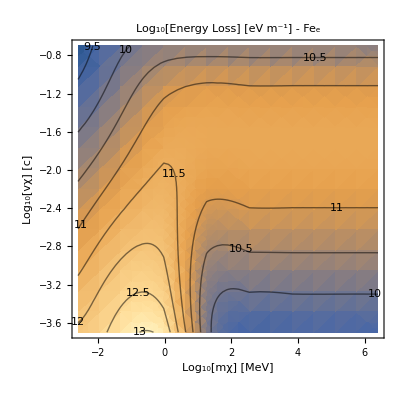

```mathematica
EnergyLoss`PlotEL[FeELOutputDictSIEnhancedTest,"Fe_e"]
```

```mathematica
Log10[("vF")/("c")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.25085,-2.16217,-2.04363,-1.7555,-1.05023,-0.388879}

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

{1.07836,1.21138,1.38919,1.82139,2.87928,3.87131}

So transition happens around the plasmon energy - weight no it doesn’t this is eV

```mathematica
Log10[("ℏ""ωp")/("JpereV")/.FeELOutputDictSIEnhanced[["fitparams"]]]
```

#### Run SiO2

```mathematica
("β")^-1/("kB")/.SiO2Totalparams
```

{290.,290.}

```mathematica
SiO2ELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2ELOutputDictSIEnhanced"]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000175393 
Prefactor:	2.08918×10^15
dEdr:	3.66428×10^11

$Aborted

```mathematica
SiO2ELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparams,True,"SiO2ELOutputDictSIEnhanced"]
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000175393 
Prefactor:	2.08918×10^15
dEdr:	3.66428×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.00006384 and 2.53169×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.00006384 
Prefactor:	2.77438×10^15
dEdr:	1.77116×10^11

dEdr total: 5.43545×10^11

2 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.001771 and 0.0000717928 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.001771 
Prefactor:	2.08918×10^13
dEdr:	3.69994×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000631085 and 0.0000248038 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000631085 
Prefactor:	2.77438×10^13
dEdr:	1.75087×10^10

dEdr total: 5.45081×10^10

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0172835 
Prefactor:	2.08918×10^11
dEdr:	3.61084×10^9

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.00660997 
Prefactor:	2.77438×10^11
dEdr:	1.83385×10^9

dEdr total: 5.44469×10^9

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.327776 
Prefactor:	2.08918×10^9
dEdr:	6.84785×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.079298 
Prefactor:	2.77438×10^9
dEdr:	2.20003×10^8

dEdr total: 9.04787×10^8

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000797277 
Prefactor:	2.08918×10^15
dEdr:	1.66566×10^12

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000305998 
Prefactor:	2.77438×10^15
dEdr:	8.48955×10^11

dEdr total: 2.51461×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00796714 
Prefactor:	2.08918×10^13
dEdr:	1.66448×10^11

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00305899 
Prefactor:	2.77438×10^13
dEdr:	8.4868×10^10

dEdr total: 2.51316×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.076435 
Prefactor:	2.08918×10^11
dEdr:	1.59687×10^10

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0297862 
Prefactor:	2.77438×10^11
dEdr:	8.26381×10^9

dEdr total: 2.42325×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.961386 
Prefactor:	2.08918×10^9
dEdr:	2.00851×10^9

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.454893 
Prefactor:	2.77438×10^9
dEdr:	1.26205×10^9

dEdr total: 3.27056×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000992502 
Prefactor:	2.08918×10^15
dEdr:	2.07352×10^12

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000394726 
Prefactor:	2.77438×10^15
dEdr:	1.09512×10^12

dEdr total: 3.16864×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0107805 
Prefactor:	2.08918×10^13
dEdr:	2.25224×10^11

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00406926 
Prefactor:	2.77438×10^13
dEdr:	1.12897×10^11

dEdr total: 3.3812×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.468181 
Prefactor:	2.08918×10^11
dEdr:	9.78116×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.144233 
Prefactor:	2.77438×10^11
dEdr:	4.00158×10^10

dEdr total: 1.37827×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.45001 
Prefactor:	2.08918×10^9
dEdr:	3.02933×10^9

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.74311 
Prefactor:	2.77438×10^9
dEdr:	2.06167×10^9

dEdr total: 5.091×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.97971×10^-6 
Prefactor:	2.08918×10^15
dEdr:	6.22515×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.07087×10^-6 
Prefactor:	2.77438×10^15
dEdr:	2.97099×10^9

dEdr total: 9.19613×10^9

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00125824 
Prefactor:	2.08918×10^13
dEdr:	2.62869×10^10

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000214061 
Prefactor:	2.77438×10^13
dEdr:	5.93885×10^9

dEdr total: 3.22257×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.477385 
Prefactor:	2.08918×10^11
dEdr:	9.97344×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.147334 
Prefactor:	2.77438×10^11
dEdr:	4.08761×10^10

dEdr total: 1.4061×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.45363 
Prefactor:	2.08918×10^9
dEdr:	3.03689×10^9

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.745309 
Prefactor:	2.77438×10^9
dEdr:	2.06777×10^9

dEdr total: 5.10466×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.27123×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.65582×10^9

For mχ = 6.18325×10^-28 , vχ = 60000
L:	2.16379×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.00318×10^8

dEdr total: 3.25614×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0013328 
Prefactor:	2.08918×10^13
dEdr:	2.78447×10^10

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000229303 
Prefactor:	2.77438×10^13
dEdr:	6.36173×10^9

dEdr total: 3.42064×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.479441 
Prefactor:	2.08918×10^11
dEdr:	1.00164×10^11

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.148592 
Prefactor:	2.77438×10^11
dEdr:	4.12251×10^10

dEdr total: 1.41389×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.4554 
Prefactor:	2.08918×10^9
dEdr:	3.0406×10^9

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.746355 
Prefactor:	2.77438×10^9
dEdr:	2.07067×10^9

dEdr total: 5.11127×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.32068×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.75914×10^9

For mχ = 1.1938×10^-26 , vχ = 60000
L:	2.28052×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.32703×10^8

dEdr total: 3.39184×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00133819 
Prefactor:	2.08918×10^13
dEdr:	2.79573×10^10

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000230744 
Prefactor:	2.77438×10^13
dEdr:	6.40172×10^9

dEdr total: 3.4359×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.479552 
Prefactor:	2.08918×10^11
dEdr:	1.00187×10^11

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.14866 
Prefactor:	2.77438×10^11
dEdr:	4.1244×10^10

dEdr total: 1.41431×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.4555 
Prefactor:	2.08918×10^9
dEdr:	3.0408×10^9

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.746411 
Prefactor:	2.77438×10^9
dEdr:	2.07083×10^9

dEdr total: 5.11163×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.32366×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.76537×10^9

For mχ = 2.30487×10^-25 , vχ = 60000
L:	2.28838×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.34883×10^8

dEdr total: 3.40025×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00133847 
Prefactor:	2.08918×10^13
dEdr:	2.79632×10^10

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000230821 
Prefactor:	2.77438×10^13
dEdr:	6.40384×10^9

dEdr total: 3.4367×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.479557 
Prefactor:	2.08918×10^11
dEdr:	1.00188×10^11

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.148664 
Prefactor:	2.77438×10^11
dEdr:	4.1245×10^10

dEdr total: 1.41433×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.4555 
Prefactor:	2.08918×10^9
dEdr:	3.04081×10^9

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.746414 
Prefactor:	2.77438×10^9
dEdr:	2.07084×10^9

dEdr total: 5.11165×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.32382×10^-6 
Prefactor:	2.08918×10^15
dEdr:	2.76569×10^9

For mχ = 4.45×10^-24 , vχ = 60000
L:	2.28879×10^-7 
Prefactor:	2.77438×10^15
dEdr:	6.34997×10^8

dEdr total: 3.40069×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00133849 
Prefactor:	2.08918×10^13
dEdr:	2.79635×10^10

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000230825 
Prefactor:	2.77438×10^13
dEdr:	6.40395×10^9

dEdr total: 3.43674×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.479558 
Prefactor:	2.08918×10^11
dEdr:	1.00188×10^11

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.148664 
Prefactor:	2.77438×10^11
dEdr:	4.1245×10^10

dEdr total: 1.41433×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.4555 
Prefactor:	2.08918×10^9
dEdr:	3.04081×10^9

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.746414 
Prefactor:	2.77438×10^9
dEdr:	2.07084×10^9

dEdr total: 5.11165×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{5.43545×10^11,5.45081×10^10,5.44469×10^9,9.04787×10^8},{2.51461×10^12,2.51316×10^11,2.42325×10^10,3.27056×10^9},{3.16864×10^12,3.3812×10^11,1.37827×10^11,5.091×10^9},{9.19613×10^9,3.22257×10^10,1.4061×10^11,5.10466×10^9},{3.25614×10^9,3.42064×10^10,1.41389×10^11,5.11127×10^9},{3.39184×10^9,3.4359×10^10,1.41431×10^11,5.11163×10^9},{3.40025×10^9,3.4367×10^10,1.41433×10^11,5.11165×10^9},{3.40069×10^9,3.43674×10^10,1.41433×10^11,5.11165×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0}},fname→SiO2ELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{242.045,439.336,423.277,464.717},{10.8898,10.3367,14.9445,83.4077},{11.1538,12.1486,25.7176,223.783},{13.6816,17.5637,19.0839,139.819},{30.42,12.5462,17.9399,106.281},{22.4367,10.8751,17.0468,105.265},{25.1557,10.9617,17.0969,114.078},{23.1409,10.1744,17.4177,113.144}},totalTime→2805.89|>

#### Plot SiO2

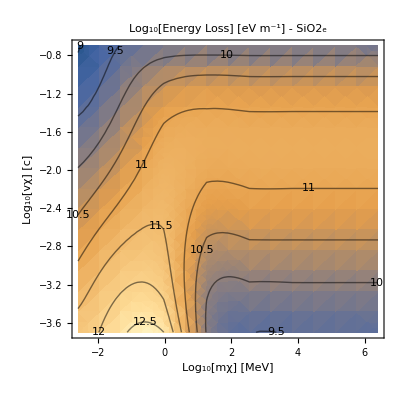

```mathematica
EnergyLoss`PlotEL[SiO2ELOutputDictSIEnhanced,"SiO2_e"]
```

```mathematica
Log10[("vF")/("c")/.SiO2ELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.05304,-1.8217}

#### Run MgO

```mathematica
MgOELOutputDictSIEnhanced = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparams,True,"MgOELOutputDictSIEnhanced"]
```

1 of 32

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000337559 and 4.38616×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000337559 
Prefactor:	3.99192×10^13
dEdr:	1.34751×10^10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1983.01}. NIntegrate obtained 0.000208341 and 1.08951×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000208341 
Prefactor:	5.73915×10^14
dEdr:	1.1957×10^11

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {3559.6}. NIntegrate obtained 0.000182741 and 4.01308×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000182741 
Prefactor:	4.00973×10^14
dEdr:	7.32741×10^10

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.0000668434 
Prefactor:	1.00279×10^16
dEdr:	6.703×10^11

dEdr total: 8.76619×10^11

2 of 32

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00337213 
Prefactor:	3.99192×10^11
dEdr:	1.34613×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00214005 
Prefactor:	5.73915×10^12
dEdr:	1.22821×10^10

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.00183626 
Prefactor:	4.00973×10^12
dEdr:	7.36293×10^9

For mχ = 4.45×10^-33 , vχ = 600000
L:	0.000596438 
Prefactor:	1.00279×10^14
dEdr:	5.98103×10^10

dEdr total: 8.08015×10^10

3 of 32

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0339014 
Prefactor:	3.99192×10^9
dEdr:	1.35332×10^8

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.0208949 
Prefactor:	5.73915×10^10
dEdr:	1.19919×10^9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.018411 
Prefactor:	4.00973×10^10
dEdr:	7.38233×10^8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

For mχ = 4.45×10^-33 , vχ = 6000000
L:	0.006315 
Prefactor:	1.00279×10^12
dEdr:	6.33263×10^9

dEdr total: 8.40538×10^9

4 of 32

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.688955 
Prefactor:	3.99192×10^7
dEdr:	2.75026×10^7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.420291 
Prefactor:	5.73915×10^8
dEdr:	2.41211×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.370221 
Prefactor:	4.00973×10^8
dEdr:	1.48449×10^8

For mχ = 4.45×10^-33 , vχ = 60000000
L:	0.0834964 
Prefactor:	1.00279×10^10
dEdr:	8.37294×10^8

dEdr total: 1.25446×10^9

5 of 32

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.00154969 
Prefactor:	3.99192×10^13
dEdr:	6.18623×10^10

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000950025 
Prefactor:	5.73915×10^14
dEdr:	5.45234×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000848748 
Prefactor:	4.00973×10^14
dEdr:	3.40325×10^11

For mχ = 8.5916×10^-32 , vχ = 60000
L:	0.000302277 
Prefactor:	1.00279×10^16
dEdr:	3.03121×10^12

dEdr total: 3.97863×10^12

6 of 32

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.0154786 
Prefactor:	3.99192×10^11
dEdr:	6.17895×10^9

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00949283 
Prefactor:	5.73915×10^12
dEdr:	5.44808×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00848144 
Prefactor:	4.00973×10^12
dEdr:	3.40083×10^10

For mχ = 8.5916×10^-32 , vχ = 600000
L:	0.00302172 
Prefactor:	1.00279×10^14
dEdr:	3.03015×10^11

dEdr total: 3.97683×10^11

7 of 32

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.14523 
Prefactor:	3.99192×10^9
dEdr:	5.79748×10^8

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.0894217 
Prefactor:	5.73915×10^10
dEdr:	5.13205×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.080161 
Prefactor:	4.00973×10^10
dEdr:	3.21424×10^9

For mχ = 8.5916×10^-32 , vχ = 6000000
L:	0.029554 
Prefactor:	1.00279×10^12
dEdr:	2.96365×10^10

dEdr total: 3.85625×10^10

8 of 32

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.55492 
Prefactor:	3.99192×10^7
dEdr:	6.20714×10^7

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	1.07773 
Prefactor:	5.73915×10^8
dEdr:	6.18526×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.989519 
Prefactor:	4.00973×10^8
dEdr:	3.9677×10^8

For mχ = 8.5916×10^-32 , vχ = 60000000
L:	0.455491 
Prefactor:	1.00279×10^10
dEdr:	4.56763×10^9

dEdr total: 5.64499×10^9

9 of 32

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00167282 
Prefactor:	3.99192×10^13
dEdr:	6.67777×10^10

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.00102198 
Prefactor:	5.73915×10^14
dEdr:	5.86528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000910984 
Prefactor:	4.00973×10^14
dEdr:	3.6528×10^11

For mχ = 1.65878×10^-30 , vχ = 60000
L:	0.000477238 
Prefactor:	1.00279×10^16
dEdr:	4.7857×10^12

dEdr total: 5.80429×10^12

10 of 32

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0195732 
Prefactor:	3.99192×10^11
dEdr:	7.81349×10^9

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.0112008 
Prefactor:	5.73915×10^12
dEdr:	6.4283×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00987762 
Prefactor:	4.00973×10^12
dEdr:	3.96066×10^10

For mχ = 1.65878×10^-30 , vχ = 600000
L:	0.00491014 
Prefactor:	1.00279×10^14
dEdr:	4.92384×10^11

dEdr total: 6.04087×10^11

11 of 32

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.889273 
Prefactor:	3.99192×10^9
dEdr:	3.54991×10^9

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.564989 
Prefactor:	5.73915×10^10
dEdr:	3.24256×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.505175 
Prefactor:	4.00973×10^10
dEdr:	2.02562×10^10

For mχ = 1.65878×10^-30 , vχ = 6000000
L:	0.148432 
Prefactor:	1.00279×10^12
dEdr:	1.48846×10^11

dEdr total: 2.05078×10^11

12 of 32

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	2.23428 
Prefactor:	3.99192×10^7
dEdr:	8.91907×10^7

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.58689 
Prefactor:	5.73915×10^8
dEdr:	9.10741×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	1.46595 
Prefactor:	4.00973×10^8
dEdr:	5.87806×10^8

For mχ = 1.65878×10^-30 , vχ = 60000000
L:	0.766219 
Prefactor:	1.00279×10^10
dEdr:	7.68358×10^9

dEdr total: 9.27131×10^9

13 of 32

For mχ = 3.2026×10^-29 , vχ = 60000
L:	5.18221×10^-6 
Prefactor:	3.99192×10^13
dEdr:	2.0687×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.73418×10^-6 
Prefactor:	5.73915×10^14
dEdr:	1.56919×10^9

For mχ = 3.2026×10^-29 , vχ = 60000
L:	2.37642×10^-6 
Prefactor:	4.00973×10^14
dEdr:	9.52881×10^8

For mχ = 3.2026×10^-29 , vχ = 60000
L:	1.52113×10^-6 
Prefactor:	1.00279×10^16
dEdr:	1.52537×10^10

dEdr total: 1.79827×10^10

14 of 32

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00326769 
Prefactor:	3.99192×10^11
dEdr:	1.30444×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.00122198 
Prefactor:	5.73915×10^12
dEdr:	7.01313×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000972574 
Prefactor:	4.00973×10^12
dEdr:	3.89976×10^9

For mχ = 3.2026×10^-29 , vχ = 600000
L:	0.000354509 
Prefactor:	1.00279×10^14
dEdr:	3.55499×10^10

dEdr total: 4.77672×10^10

15 of 32

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.898256 
Prefactor:	3.99192×10^9
dEdr:	3.58577×10^9

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.574123 
Prefactor:	5.73915×10^10
dEdr:	3.29498×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.514572 
Prefactor:	4.00973×10^10
dEdr:	2.0633×10^10

For mχ = 3.2026×10^-29 , vχ = 6000000
L:	0.147888 
Prefactor:	1.00279×10^12
dEdr:	1.48301×10^11

dEdr total: 2.0547×10^11

16 of 32

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	2.23944 
Prefactor:	3.99192×10^7
dEdr:	8.93967×10^7

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.59063 
Prefactor:	5.73915×10^8
dEdr:	9.1289×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	1.46945 
Prefactor:	4.00973×10^8
dEdr:	5.89211×10^8

For mχ = 3.2026×10^-29 , vχ = 60000000
L:	0.768635 
Prefactor:	1.00279×10^10
dEdr:	7.70781×10^9

dEdr total: 9.2993×10^9

17 of 32

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.22165×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.28606×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	1.22057×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.00503×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	9.73437×10^-7 
Prefactor:	4.00973×10^14
dEdr:	3.90322×10^8

For mχ = 6.18325×10^-28 , vχ = 60000
L:	3.61604×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.62614×10^9

dEdr total: 4.84557×10^9

18 of 32

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00343064 
Prefactor:	3.99192×10^11
dEdr:	1.36948×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.0012945 
Prefactor:	5.73915×10^12
dEdr:	7.42932×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.00103241 
Prefactor:	4.00973×10^12
dEdr:	4.1397×10^9

For mχ = 6.18325×10^-28 , vχ = 600000
L:	0.000378692 
Prefactor:	1.00279×10^14
dEdr:	3.79749×10^10

dEdr total: 5.09134×10^10

19 of 32

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.900914 
Prefactor:	3.99192×10^9
dEdr:	3.59638×10^9

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.576212 
Prefactor:	5.73915×10^10
dEdr:	3.30697×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.516556 
Prefactor:	4.00973×10^10
dEdr:	2.07125×10^10

For mχ = 6.18325×10^-28 , vχ = 6000000
L:	0.149062 
Prefactor:	1.00279×10^12
dEdr:	1.49478×10^11

dEdr total: 2.06857×10^11

20 of 32

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	2.24101 
Prefactor:	3.99192×10^7
dEdr:	8.94595×10^7

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.59248 
Prefactor:	5.73915×10^8
dEdr:	9.13951×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	1.47118 
Prefactor:	4.00973×10^8
dEdr:	5.89905×10^8

For mχ = 6.18325×10^-28 , vχ = 60000000
L:	0.769763 
Prefactor:	1.00279×10^10
dEdr:	7.71911×10^9

dEdr total: 9.31243×10^9

21 of 32

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.32264×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32637×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.26762×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.27504×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	1.01275×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.06084×10^8

For mχ = 1.1938×10^-26 , vχ = 60000
L:	3.79569×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.80629×10^9

dEdr total: 5.07251×10^9

22 of 32

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00344154 
Prefactor:	3.99192×10^11
dEdr:	1.37384×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00129973 
Prefactor:	5.73915×10^12
dEdr:	7.45935×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.00103683 
Prefactor:	4.00973×10^12
dEdr:	4.15741×10^9

For mχ = 1.1938×10^-26 , vχ = 600000
L:	0.000380819 
Prefactor:	1.00279×10^14
dEdr:	3.81882×10^10

dEdr total: 5.11788×10^10

23 of 32

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.901058 
Prefactor:	3.99192×10^9
dEdr:	3.59695×10^9

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.576324 
Prefactor:	5.73915×10^10
dEdr:	3.30761×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.516663 
Prefactor:	4.00973×10^10
dEdr:	2.07168×10^10

For mχ = 1.1938×10^-26 , vχ = 6000000
L:	0.149126 
Prefactor:	1.00279×10^12
dEdr:	1.49543×10^11

dEdr total: 2.06932×10^11

24 of 32

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	2.24204 
Prefactor:	3.99192×10^7
dEdr:	8.95005×10^7

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14009×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89942×10^8

For mχ = 1.1938×10^-26 , vχ = 60000000
L:	0.769823 
Prefactor:	1.00279×10^10
dEdr:	7.71972×10^9

dEdr total: 9.31318×10^9

25 of 32

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.32846×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.3287×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.27043×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29119×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	1.01512×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07037×10^8

For mχ = 2.30487×10^-25 , vχ = 60000
L:	3.8075×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81813×10^9

dEdr total: 5.08715×10^9

26 of 32

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00344211 
Prefactor:	3.99192×10^11
dEdr:	1.37406×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00130001 
Prefactor:	5.73915×10^12
dEdr:	7.46093×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.00103706 
Prefactor:	4.00973×10^12
dEdr:	4.15834×10^9

For mχ = 2.30487×10^-25 , vχ = 600000
L:	0.000380932 
Prefactor:	1.00279×10^14
dEdr:	3.81995×10^10

dEdr total: 5.11929×10^10

27 of 32

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.901065 
Prefactor:	3.99192×10^9
dEdr:	3.59698×10^9

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.57633 
Prefactor:	5.73915×10^10
dEdr:	3.30765×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.516669 
Prefactor:	4.00973×10^10
dEdr:	2.0717×10^10

For mχ = 2.30487×10^-25 , vχ = 6000000
L:	0.14913 
Prefactor:	1.00279×10^12
dEdr:	1.49546×10^11

dEdr total: 2.06936×10^11

28 of 32

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	2.24184 
Prefactor:	3.99192×10^7
dEdr:	8.94926×10^7

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14012×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89945×10^8

For mχ = 2.30487×10^-25 , vχ = 60000000
L:	0.769827 
Prefactor:	1.00279×10^10
dEdr:	7.71976×10^9

dEdr total: 9.31321×10^9

29 of 32

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.32876×10^-6 
Prefactor:	3.99192×10^13
dEdr:	1.32882×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.27058×10^-6 
Prefactor:	5.73915×10^14
dEdr:	7.29204×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	1.01525×10^-6 
Prefactor:	4.00973×10^14
dEdr:	4.07086×10^8

For mχ = 4.45×10^-24 , vχ = 60000
L:	3.80812×10^-7 
Prefactor:	1.00279×10^16
dEdr:	3.81875×10^9

dEdr total: 5.08792×10^9

30 of 32

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00344214 
Prefactor:	3.99192×10^11
dEdr:	1.37408×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00130002 
Prefactor:	5.73915×10^12
dEdr:	7.46101×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.00103707 
Prefactor:	4.00973×10^12
dEdr:	4.15839×10^9

For mχ = 4.45×10^-24 , vχ = 600000
L:	0.000380938 
Prefactor:	1.00279×10^14
dEdr:	3.82001×10^10

dEdr total: 5.11936×10^10

31 of 32

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.901066 
Prefactor:	3.99192×10^9
dEdr:	3.59698×10^9

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.57633 
Prefactor:	5.73915×10^10
dEdr:	3.30765×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.516669 
Prefactor:	4.00973×10^10
dEdr:	2.0717×10^10

For mχ = 4.45×10^-24 , vχ = 6000000
L:	0.14913 
Prefactor:	1.00279×10^12
dEdr:	1.49546×10^11

dEdr total: 2.06937×10^11

32 of 32

For mχ = 4.45×10^-24 , vχ = 60000000
L:	2.24184 
Prefactor:	3.99192×10^7
dEdr:	8.94926×10^7

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.59259 
Prefactor:	5.73915×10^8
dEdr:	9.14012×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.47128 
Prefactor:	4.00973×10^8
dEdr:	5.89944×10^8

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.769827 
Prefactor:	1.00279×10^10
dEdr:	7.71976×10^9

dEdr total: 9.31321×10^9

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{8.76619×10^11,8.08015×10^10,8.40538×10^9,1.25446×10^9},{3.97863×10^12,3.97683×10^11,3.85625×10^10,5.64499×10^9},{5.80429×10^12,6.04087×10^11,2.05078×10^11,9.27131×10^9},{1.79827×10^10,4.77672×10^10,2.0547×10^11,9.2993×10^9},{4.84557×10^9,5.09134×10^10,2.06857×10^11,9.31243×10^9},{5.07251×10^9,5.11788×10^10,2.06932×10^11,9.31318×10^9},{5.08715×10^9,5.11929×10^10,2.06936×10^11,9.31321×10^9},{5.08792×10^9,5.11936×10^10,2.06937×10^11,9.31321×10^9}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.50385×10^29,qF→1.64516×10^10,vF→1.90521×10^6,μ→1.65338×10^-18,ωp→2.18914×10^16,α→1/137,χ→0.604859,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→412.839,nI→1.87981×10^28,Z→8,M→9.27329×10^-26,EF→1.65338×10^-18,ωi→2.18914×10^16,νi→4.25006×10^15,Ai→0.039834,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→3.58115×10^29,qF→2.19692×10^10,vF→2.54418×10^6,μ→2.94839×10^-18,ωp→3.37819×10^16,α→1/137,χ→0.523421,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→736.197,nI→4.47644×10^28,Z→8,M→9.27329×10^-26,EF→2.94839×10^-18,ωi→3.37819×10^16,νi→5.06751×10^15,Ai→0.180092,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.37351×10^29,qF→2.34828×10^10,vF→2.71947×10^6,μ→3.36866×10^-18,ωp→3.73325×10^16,α→1/137,χ→0.506271,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→841.135,nI→5.46689×10^28,Z→8,M→9.27329×10^-26,EF→3.36866×10^-18,ωi→3.73325×10^16,νi→5.23006×10^15,Ai→0.0963866,ωedgei→0},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.61838×10^30,qF→3.63218×10^10,vF→4.20631×10^6,μ→8.05919×10^-18,ωp→7.18146×10^16,α→1/137,χ→0.407075,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2012.33,nI→2.02298×10^29,Z→8,M→9.27329×10^-26,EF→8.05919×10^-18,ωi→7.18146×10^16,νi→1.12397×10^17,Ai→0.421157,ωedgei→0}},fname→MgOELOutputDictSIEnhanced,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{986.281,1532.73,1432.49,915.526},{23.9448,31.1745,55.902,264.427},{22.9495,32.4782,109.425,437.84},{37.8147,48.8602,77.9548,450.938},{69.0436,37.8296,77.926,380.519},{63.4725,33.6695,75.334,354.165},{63.3948,33.62,74.725,365.064},{61.6086,32.191,74.2328,363.928}},totalTime→8621.46|>

#### Plot MgO

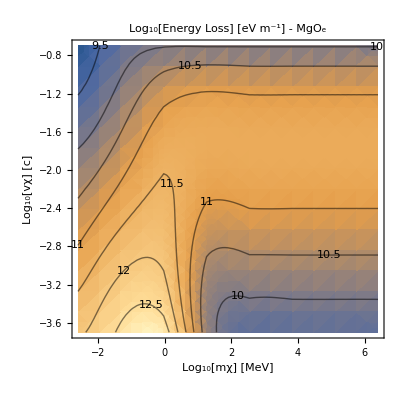

```mathematica
EnergyLoss`PlotEL[MgOELOutputDictSIEnhanced,"MgO_e"]
```

```mathematica
Log10[("vF")/("c")/.MgOELOutputDictSIEnhanced[["fitparams"]]]
```

{-2.19718,-2.07157,-2.04264,-1.85322}

### Find fraction of silicate energy loss below the band gap

Here we investigate the fraction of the contribution to the energy loss from part of the phase space below the band gap in the silicates, since our use of the optical data there is questionable. This is a check of our approximation.

bbg suffixes stand for below band gap

#### Run SiO2

```mathematica
(*ωbgSiO2 = 8.90 ("JpereV")/("ℏ")/.SIConstRepl
SiO2Totalparamsbbg = Table[Join[SiO2Totalparams[[i]],{"ωbg"->ωbgSiO2}],{i,Length[SiO2Totalparams]}]*)
```

1.35145×10^16

{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→2.0121×10^30,qF→3.90562×10^10,vF→4.52297×10^6,μ→9.3183×10^-18,ωp→8.0075×10^16,α→1/137,χ→0.392567,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→2326.72,nI→2.51512×10^29,Z→8,M→9.27329×10^-26,EF→9.3183×10^-18,ωi→8.0075×10^16,νi→6.06034×10^16,Ai→0.0871584,ωedgei→0,ωbg→1.35145×10^16}}

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^3("JpereV")/("c")^2/.SIConstRepl,2 10^-4"c" /.SIConstRepl,FeTotalparams[[1]]]*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {1987.19}. NIntegrate obtained 0.000726932 and 6.96818×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000726932 
Prefactor:	1.28051×10^14
dEdr:	9.30847×10^10

<|mχ→4.45×10^-33,vχ→60000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14},L→0.000726932,Prefactor→1.28051×10^14,dEdr→9.30847×10^10|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^7("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-29 , vχ = 60000000
L:	1.94138 
Prefactor:	2.08918×10^9
dEdr:	4.05589×10^9

<|mχ→4.45×10^-29,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94138,Prefactor→2.08918×10^9,dEdr→4.05589×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	1.94132 
Prefactor:	2.08918×10^9
dEdr:	4.05577×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→1.94132,Prefactor→2.08918×10^9,dEdr→4.05577×10^9|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`z near {EnergyLoss`Private`z} = {0.615183}. NIntegrate obtained 0.00496808 and 5.55222×10^-6 for the integral and error estimates.

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.00496808 
Prefactor:	2.08918×10^9
dEdr:	1.03792×10^7

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→1.35145×10^16},L→0.00496808,Prefactor→2.08918×10^9,dEdr→1.03792×10^7|>

```mathematica
(*EnergyLossMSIFitEnhanced[2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,ReplaceParams[SiO2Totalparamsbbg[[1]],10^20,"ωbg"]]*)
```

For mχ = 4.45×10^-24 , vχ = 60000000
L:	0.970659 
Prefactor:	2.08918×10^9
dEdr:	2.02788×10^9

<|mχ→4.45×10^-24,vχ→60000000,fitparams→{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→2.49694×10^20,ne→4.07027×10^29,qF→2.2927×10^10,vF→2.65511×10^6,μ→3.21109×10^-18,ωp→3.60151×10^16,α→1/137,χ→0.512371,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→801.791,nI→5.08784×10^28,Z→8,M→9.27329×10^-26,EF→3.21109×10^-18,ωi→3.60151×10^16,νi→2.11534×10^16,Ai→0.552697,ωedgei→0,ωbg→100000000000000000000},L→0.970659,Prefactor→2.08918×10^9,dEdr→2.02788×10^9|>

```mathematica
(*uMIntegralFitEnhanced[1.1,2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
(*uMIntegralFitEnhanced[0.1,2.5 10^12("JpereV")/("c")^2/.SIConstRepl,2 10^-1"c" /.SIConstRepl,SiO2Totalparamsbbg[[1]]]*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in EnergyLoss`Private`u near {EnergyLoss`Private`u} = {1.14685}. NIntegrate obtained 0.101876 and 0.00187779 for the integral and error estimates.

0.101876

```mathematica
(*HeavisideTheta[(("ℏ""ωbg")/(z 4"EF")-Abs[u])/.SiO2Totalparamsbbg[[1]]]/.u->(0.1"c"/"vF"/.SiO2Totalparamsbbg[[1]])*)
```

HeavisideTheta[-11.299+0.111004/z]

```mathematica
(*0.1"c"/"vF"/.SiO2Totalparamsbbg[[1]]*)
```

11.299

```mathematica
(*SiO2ELOutputDictSIEnhancedbbg = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,SiO2Totalparamsbbg,True,"SiO2ELOutputDictSIEnhancedbbg"]*)
```

1 of 32

For mχ = 4.45×10^-33 , vχ = 60000
L:	0.000351525 
Prefactor:	2.08918×10^15
dEdr:	7.344×10^11

$Aborted

#### Plot SiO2

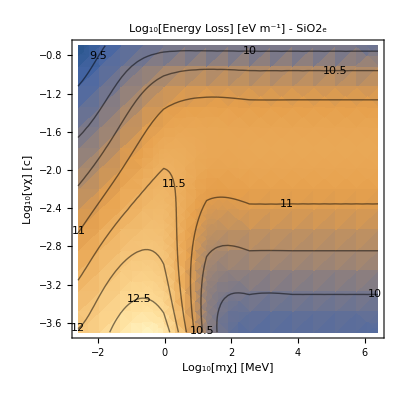

```mathematica
(*EnergyLoss`PlotEL[SiO2ELOutputDictSIEnhancedbbg,"SiO2_e"]*)
```

#### Run MgO

```mathematica
(*ωbgMgO = 7.77("JpereV")/("ℏ")/.SIConstRepl
MgOTotalparamsbbg = Table[Join[MgOTotalparams[[i]],{"ωbg"->ωbgMgO}],{i,Length[MgOTotalparams]}]*)
```

```mathematica
(*MgOELOutputDictSIEnhancedbbg = EnergyLossTableAndInterFITTotalParamsEnhanced[{2.5 10^3,2.5 10^12} ("JpereV")/("c")^2/.SIConstRepl,{2 10^-4,2 10^-1} "c" /.SIConstRepl,<|"mχ"->8,"vχ"->4|>,MgOTotalparamsbbg,True,"MgOELOutputDictSIEnhancedbbg"]*)
```

1 of 32

dEdr total: 0

2 of 32

dEdr total: 0

3 of 32

dEdr total: 0

4 of 32

dEdr total: 0

5 of 32

dEdr total: 0

6 of 32

dEdr total: 0

7 of 32

dEdr total: 0

8 of 32

dEdr total: 0

9 of 32

dEdr total: 0

10 of 32

dEdr total: 0

11 of 32

dEdr total: 0

12 of 32

dEdr total: 0

13 of 32

dEdr total: 0

14 of 32

dEdr total: 0

15 of 32

dEdr total: 0

16 of 32

dEdr total: 0

17 of 32

dEdr total: 0

18 of 32

dEdr total: 0

19 of 32

dEdr total: 0

20 of 32

dEdr total: 0

21 of 32

dEdr total: 0

22 of 32

dEdr total: 0

23 of 32

dEdr total: 0

24 of 32

dEdr total: 0

25 of 32

dEdr total: 0

26 of 32

dEdr total: 0

27 of 32

dEdr total: 0

28 of 32

dEdr total: 0

29 of 32

dEdr total: 0

30 of 32

dEdr total: 0

31 of 32

dEdr total: 0

32 of 32

dEdr total: 0

<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},fitparams→MgOTotalparamsbbg,fname→MgOELOutputDictSIEnhancedbbg,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{0.0001934,0.0001361,0.0001289,0.0001244},{0.0001242,0.0001286,0.0001263,0.000118},{0.0001233,0.0001277,0.0001226,0.0001156},{0.0001188,0.0001211,0.0001243,0.000137},{0.000132,0.0001281,0.0001271,0.0001241},{0.0001301,0.000122,0.0001225,0.0001274},{0.0001256,0.0001391,0.0001301,0.0001734},{0.0001249,0.0001405,0.0001277,0.0001282}},totalTime→0.0041731|>

#### Plot MgO

```mathematica
(*EnergyLoss`PlotEL[MgOELOutputDictSIEnhancedbbg,"MgO_e"]*)
```

Infinity::indet: Indeterminate expression -∞+∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

```mathematica
(*Log10[("vF")/("c")/.MgOELOutputDictSIEnhanced[["fitparams"]]]*)
```

{-2.19718,-2.07157,-2.04264,-1.85322}